Legendre Polynomials that satisfy following orthogonality principle
1/2∫_-1^1 ϕ^k(ξ)ϕ^l(ξ)ⅆξ = δ_kl

```mathematica
OrthogonalIntegral[k_,l_]:=1/2∫_-1^1 Subscript[ϕ, k][ξ]Subscript[ϕ, l][ξ]ⅆξ
OrthogonalQ[k_,l_]:=1/2∫_-1^1 Subscript[ϕ, k][ξ]Subscript[ϕ, l][ξ]ⅆξ==KroneckerDelta[k,l]
Subscript[ϕ, 1][ξ_]:=1;
Subscript[ϕ, 2][ξ_]:=√3 ξ;
Subscript[ϕ, 3][ξ_]:=(√5)/2 (3 ξ^2-1);
Subscript[ϕ, 4][ξ_]:=(√7)/2(5 ξ^3-3 ξ);
Subscript[ϕ, 5][ξ_]:=105/8 ξ^4+-45/4 ξ^2+9/8;
M = 5;
```

#### Solve

```mathematica
Subscript[ϕ, 3][ξ_]:=a ξ^2+ c;
Solve[{OrthogonalIntegral[1,3]==0,
OrthogonalIntegral[3,3]==1},{a,c}]
```

{{a→-(3 √5)/2,c→(√5)/2},{a→(3 √5)/2,c→-(√5)/2}}

```mathematica
Subscript[ϕ, 4][ξ_]:=a ξ^3+b ξ;
Solve[{OrthogonalIntegral[2,4]==0,OrthogonalIntegral[4,4]==1},{a,b}]
```

{{a→-(5 √7)/2,b→(3 √7)/2},{a→(5 √7)/2,b→-(3 √7)/2}}

```mathematica
Subscript[ϕ, 5][ξ_]:=a ξ^4+b ξ^2+c;
Solve[{OrthogonalIntegral[1,5]==0,OrthogonalIntegral[3,5]==0,OrthogonalIntegral[5,5]==1},{a,b,c}]
```

{{a→-105/8,b→45/4,c→-9/8},{a→105/8,b→-45/4,c→9/8}}

#### Plot

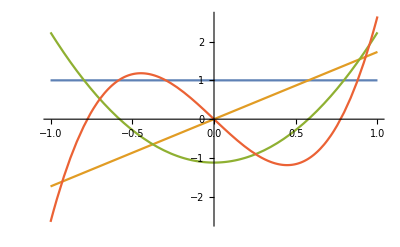

```mathematica
Plot[Evaluate[Table[Subscript[ϕ, k][ξ],{k,1,M}]],{ξ,-1,1}]
```

#### Check Orthogonality

```mathematica
Table[OrthogonalQ[i,j],{i,1,M},{j,1,M}]//TableForm
```

True | True | True | True | True
True | True | True | True | True
True | True | True | True | True
True | True | True | True | True
True | True | True | True | True

#### Integrals

```mathematica
A = Table[∫_-1^1 D[Subscript[ϕ, k][ξ],ξ]Subscript[ϕ, l][ξ]ⅆξ,{k,1,M},{l,1,M}]//TableForm//Simplify
```

0 | 0 | 0 | 0 | 0
2 √3 | 0 | 0 | 0 | 0
0 | 2 √15 | 0 | 0 | 0
2 √7 | 0 | 2 √35 | 0 | 0
0 | 6 √3 | 0 | 6 √7 | 0